# SAreapoly Lcir

Mc (-1/(a+b+c)^6+1/2 (1/a^12+1/b^12+1/c^12) (a+b+c) (-a+1/2 (a+b+c)) (-b+1/2 (a+b+c)) (-c+1/2 (a+b+c)) VSC)

4/(2187 Rc^2)

{{Mc→2916}}

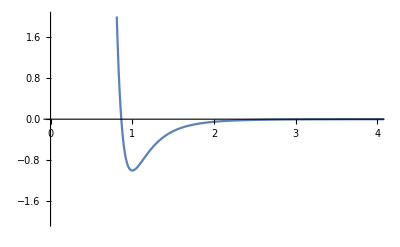

```mathematica
s = (a+b+c)/2;
area2 = s*(s-a)*(s-b)*(s-c);

Vshort = area2*(a^-12+b^-12+c^-12);
Vlong = - 1/(a+b+c)^6;

Vtotal = Mc*(Vlong+VSC*Vshort)
Vtri = Vtotal/.{a->r/Rc, b->r/Rc, c->r/Rc};

minRsol = (r/.Solve[D[Vtri,r]==0,r][[2]][[1]]);
VSCsol = VSC/.Solve[minRsol==1,VSC][[1]][[1]]

Solve[(Vtri/.{r->minRsol}/.{VSC->VSCsol}/.{Rc->1})==-1, Mc]

Plot[(Vtri/.{VSC->VSCsol})/.{Mc->2916,Rc->1},{r,0,5}, PlotRange->{{0, 4}, {-2, 2}}]
```

# SAreacir Lcir

Mc (-1/(a+b+c)^6+((-a+1/2 (a+b+c)) (-b+1/2 (a+b+c)) (-c+1/2 (a+b+c)) VSC)/(2 (a+b+c)^11))

2916/Rc^2

{{Mc→2916}}

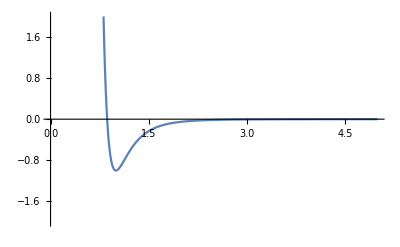

```mathematica
s = (a+b+c)/2;
area2 = s*(s-a)*(s-b)*(s-c);

Vshort = area2*((a+b+c)^-12);
Vlong = - 1/(a+b+c)^6;

Vtotal = Mc*(Vlong+VSC*Vshort)
Vtri = Vtotal/.{a->r/Rc, b->r/Rc, c->r/Rc};

minRsol = (r/.Solve[D[Vtri,r]==0,r][[2]][[1]]);
VSCsol = VSC/.Solve[minRsol==1,VSC][[1]][[1]]

Solve[(Vtri/.{r->minRsol}/.{VSC->VSCsol}/.{Rc->1})==-1, Mc]

Plot[(Vtri/.{VSC->VSCsol})/.{Mc->2916,Rc->1},{r,0,5}, PlotRange->{{0, 5}, {-2, 2}}]
```

# SPoly Lareacir

Mc (-(√((a+b+c) (-a+1/2 (a+b+c)) (-b+1/2 (a+b+c)) (-c+1/2 (a+b+c))))/(√2 (a+b+c)^6)+(1/a^12+1/b^12+1/c^12) VSC)

1/(8748 √3 Rc^8)

{{Mc→-1458 √3}}

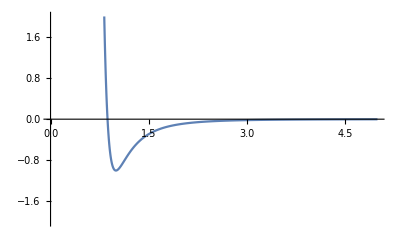

```mathematica
s = (a+b+c)/2;
area2 = s*(s-a)*(s-b)*(s-c);

Vshort = (a^-12+b^-12+c^-12);
Vlong = - 1*Sqrt[area2]/(a+b+c)^6;

Vtotal = Mc*(Vlong+VSC*Vshort)
Vtri = Vtotal/.{a->r/Rc, b->r/Rc, c->r/Rc};

minRsol = (r/.Solve[D[Vtri,r]==0,r][[2]][[1]]);
VSCsol = VSC/.Solve[minRsol==1,VSC][[1]][[1]]

Solve[(Vtri/.{r->minRsol}/.{VSC->VSCsol}/.{Rc->1})==-1, Mc]

Plot[(Vtri/.{VSC->VSCsol})/.{Mc->1458*Sqrt[3],Rc->1},{r,0,5}, PlotRange->{{0, 5}, {-2, 2}}]
```

# SPoly LCir

Mc (-1/(a+b+c)^6+(1/a^12+1/b^12+1/c^12) VSC)

1/(4374 Rc^6)

{{Mc→1458}}

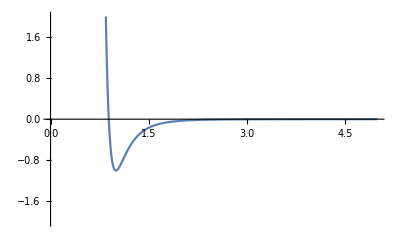

```mathematica
Vshort = a^-12+b^-12+c^-12;
Vlong = - 1/(a+b+c)^6;

Vtotal = Mc*(Vlong+VSC*Vshort)
Vtri = Vtotal/.{a->r/Rc, b->r/Rc, c->r/Rc};

minRsol = (r/.Solve[D[Vtri,r]==0,r][[2]][[1]]);
VSCsol = VSC/.Solve[minRsol==1,VSC][[1]][[1]]

Solve[(Vtri/.{r->minRsol}/.{VSC->VSCsol}/.{Rc->1})==-1, Mc]

Plot[(Vtri/.{VSC->VSCsol})/.{Mc->1458,Rc->1},{r,0,5}, PlotRange->{{0, 5}, {-2, 2}}]
```